```mathematica
A=1;
```

```mathematica
v[x_,y_]:={- A Cos[2π x] Sin[2π y],A Sin[2π x] Cos[2π y] };
```

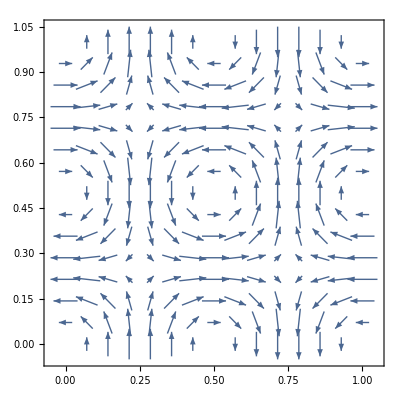

```mathematica
VectorPlot[v[x,y],{x,0,1},{y,0,1}]
```

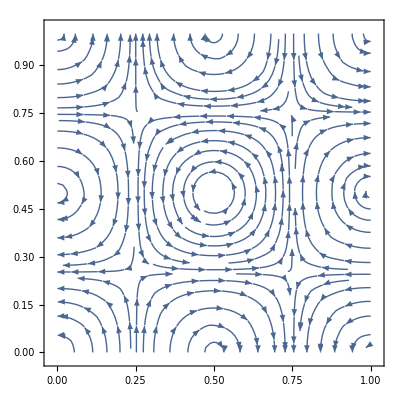

```mathematica
StreamPlot[v[x,y],{x,0,1},{y,0,1}]
```

```mathematica
Div[v[x,y],{x,y}]
```

0

```mathematica
Curl[v[x,y],{x,y}]
```

4 π Cos[2 π x] Cos[2 π y]

```mathematica
Plot3D[4 π Cos[2 π x] Cos[2 π y],{x,0,1},{y,0,1}]
```

-Graphics3D-

Question 3

```mathematica
ClearAll[A,v];
```

```mathematica
v[x_,y_]:={- A Cos[2π x] Sin[2π y],A Sin[2π x] Cos[2π y] };
```

```mathematica
v1 = v[x,y][[1]];
```

```mathematica
v2 = v[x,y][[2]];
```

```mathematica
field =  {v1 D[v1,x] + v2 D[v1,y],v1 D[v2,x] + v2 D[v2,y]}
```

{-2 A^2 π Cos[2 π x] Cos[2 π y]^2 Sin[2 π x]-2 A^2 π Cos[2 π x] Sin[2 π x] Sin[2 π y]^2,-2 A^2 π Cos[2 π x]^2 Cos[2 π y] Sin[2 π y]-2 A^2 π Cos[2 π y] Sin[2 π x]^2 Sin[2 π y]}

```mathematica
fielSimplified = FullSimplify[field]
```

{-A^2 π Sin[4 π x],-A^2 π Sin[4 π y]}

```mathematica
fielSimplified/.{A->1}
```

{-π Sin[4 π x],-π Sin[4 π y]}

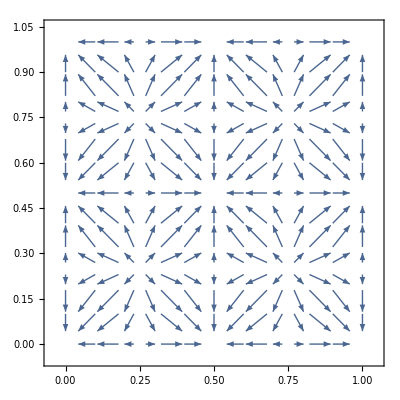

```mathematica
VectorPlot[fielSimplified/.{A->1},{x,0,1},{y,0,1}]
```